# WWP First Isola (p=2)

CONTACT INFORMATION :
  
Ryan Creedon
Department of Applied Mathematics
University of Washington, Seattle, WA

DIRECTIONS:

To evaluate this file, click the Evaluation tab above and then Evaluate Notebook from the drop-down menu.

```mathematica
0.Notation
```

STOKES  WAVES

α : aspect ratio of dimensional Stokes waves, >0, specified by user;
ϵ : small-amplitude parameter,>0, specified by user;
c_0 : zero-amplitude Stokes wave velocity, c_0 = Sqrt[Tanh[α]];
ω : dispersion relation of nondimensional Euler equations in stationary frame, ω[k] = Sign[k]*Sqrt[k*Tanh[α*k]];
Ω : dispersion relation of nondimensional Euler equations in traveling frame,Ω[k,σ] = -c_0*k+σ*ω[k] ;
σ : indicates branch of dispersion relation, σ = +/- 1;
c_g : group velocity of nondimensional Euler equations in traveling frame, c_g[k,σ] = D[Ω[k,σ],k];
c_j : O(ϵ^j) correction of Stokes wave velocity, see Appendix A in manuscript;
η_S_j : O(ϵ^j) correction of Stokes wave surface displacement, see Appendix A in manuscript;
N_(j,k): kth complex Fourier series coefficient of η_S_j;
q_S_j : O(ϵ^j) correction of Stokes wave horizontal velocity potential along surface displacement, see Appendix A in manuscript;
Q_(j,k) : kth complex Fourier cosine series coefficient of q_S_j;

HIGH-FREQUENCY  ISOLA

p : denotes the (p-1)th isola, p=2 in this notebook;
n : integer corresponding to collided eigenvalues;
λ_j : O(ϵ^j) eigenvalue correction;
tildeλ_j : tildeλ_j = ⅈλ_j;
w_j : O(ϵ^j) eigenfunction correction;
γ_j : coefficient of nullspace component of w_j proportional to Exp[ⅈ(n+p)x];
μ_j : O(ϵ^j) Floquet exponent correction;
IHT_j : inhomogeneous forcing terms in O(ϵ^j) spectral problem;
IHT_(j,k) : gives terms proportional to Exp[ⅈkx] from IHT_j; 
ω_k : ω[μ_0+k];
c_(g_(σ,k)): c_g[μ_0+k,σ];
FA_k : vector given by Fredholm alternative to enforce solvability condition k;
s_k : Sinh[α*(μ_0+k)];
C_k : Cosh[α*(μ_0+k)];
cond_(j,k) : solvability condition k at O(ϵ^j);
partsoln_j : gives particular solution to O(ϵ^j) spectral problem as list of Fourier coefficients;
h_(j,k) : 1st component of the kth complex Fourier mode of the particular solution at O(ϵ^j),h_(j,k) = tildeh_(j,k) + γ_0*Γ_(h,j,k,0) + γ_1*Γ_(h,j,k,1) + ...;
ϕ_(j,k) : 2nd component of the kth complex Fourier mode of the particular solution at O(ϵ^j),ϕ_(j,k) = ⅈ(tildeϕ_(j,k) + γ_0*Γ_(ϕ,j,k,0) + γ_1*Γ_(ϕ,j,k,1) + ...);

```mathematica
I. Useful Functions
```

```mathematica
(* Linearized dispersion relation of WWP, Subscript[c, 0] = Sqrt[Tanh[α]]. *)

Ω[k_,σ_]:= -Subscript[c, 0]*k+σ*ω[k];
ω[k_] := Sign[k]*Sqrt[k*Tanh[α*k]];

(** nth order Floquet differentiation of f. Computes (Subscript[μ, 0]+Subscript[D, x])^n[f[x]], where Subscript[D, x] = -Subscript[ⅈd, x]. **)

Fdiff[f_,n_] := If[n==0,f,Expand[(ν-ⅈ*diff)^n] /. diff^j_ :> D[f,{x,j}] //. diff -> D[f,x]//. ν^n ->Subscript[μ, 0]^n*f //. ν -> Subscript[μ, 0]]; 

(** Expand q into a complex Fourier sum. Useful when q is a product of sinusoidal functions. **)

FourierSum[q_] := Expand[TrigToExp[q]] /. Exp[θ_]:> Exp[Simplify[θ]];

(** Creates list of complex Fourier coefficients of a generic function q without using the expensive built-in FourierCoefficient Mathematica function. Must provide a list of desired Fourier modes k. List must
be ordered from least to greatest.  **)

NCoefficient[q_,k_] := CoefficientList[Expand[ z^(-k[[1]])*(TrigToExp[q] /. Exp[θ_]:> Exp[Simplify[θ]]/. Exp[y_] :> z^(Simplify[y/ⅈ/x]))],z];

(** Generate the nth order modulation of a list of wavenumbers k. **)

GenModulate[k_,n_] :=  (Clear[S,P];
S = {}; 
For[j=1,j≤ Length[k],j++,
P = Union[S,k[[j]]+Range[-n,n]];
S = P];
P);

(** Obtain the particular solution of nth-order problem. Importantly, IHT are the inhomogeneous terms after applying the row operation {{1/Subscript[C, k[[j]]],0},{0,1}}.**)

partsoln[IHT_,k_,n_]:= (Clear[S]; S = {};
For[
j=1,
j ≤ Length[k],j++,
A = {{(ⅈ*Subscript[c, 0]*(Subscript[μ, 0]+k[[j]])-Subscript[λ, 0]),Subscript[ω, k[[j]]]^2},{-1,ⅈ*Subscript[c, 0]*(Subscript[μ, 0]+k[[j]])-Subscript[λ, 0]}};
Subscript[w, n,k[[j]]] = {Subscript[h, n,k[[j]]],Subscript[ϕ, n,k[[j]]]};
Subscript[soln, j] = Flatten[Simplify[Solve[A.Subscript[w, n,k[[j]]] - IHT[[All,j]]==0,Subscript[w, n,k[[j]]]]]];
S=Append[S,Subscript[soln, j]]];
S);
```

```mathematica
II. Zeroth-Order Problem
```

```mathematica
p=2;
Subscript[λ, 0] = Simplify[-ⅈ*(-Subscript[c, 0]*(Subscript[μ, 0]+n)+Subscript[ω, n])]

(** Collided eigenfunction, normalized so that first component has unit nth Fourier mode. 
Subscript[γ, 0] is an arbitrary constant at this order. **)

Subscript[w, 0] = {1,1/(ⅈ*Subscript[ω, n])}*Exp[ⅈ*n*x] + Subscript[γ, 0]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]

Subscript[FA, n] = {1,-ⅈ*Subscript[ω, n]}
Subscript[FA, n+p] = {1,ⅈ*Subscript[ω, n+p]}

(* Define the Subscript[L, 0] operator for computations. *)

Subscript[NumL, 0][w_,k_] := (FCoeff = NCoefficient[w,k];{ⅈ*Subscript[c, 0]*Sum[(Subscript[μ, 0]+k[[j]])*Subscript[C, k[[j]]]*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}]+Sum[(Subscript[μ, 0]+k[[j]])*Subscript[s, k[[j]]]*FCoeff[[2,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],-w[[1]]+ⅈ*Subscript[c, 0]*Fdiff[w[[2]],1]});

(* Define the Subscript[R, 0] operator for computations. *)

Subscript[NumR, 0][w_,k_]  := (FCoeff = NCoefficient[w,k];{Sum[Subscript[C, k[[j]]]*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],w[[2]]});

(* Define the Subscript[R, 0]^-1 operator for computations. *)

Subscript[NumInvR, 0][w_,k_]  := (FCoeff = NCoefficient[w,k];{Sum[1/(Subscript[C, k[[j]]])*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],w[[2]]});
```

-ⅈ (-c_0 (n+μ_0)+ω_n)

{ⅇ^(ⅈ n x)+ⅇ^(ⅈ (2+n) x) γ_0,-(ⅈ ⅇ^(ⅈ n x))/ω_n+(ⅈ ⅇ^(ⅈ (2+n) x) γ_0)/(ω_(2+n))}

{1,-ⅈ ω_n}

{1,ⅈ ω_(2+n)}

```mathematica
III. First-Order Problem
```

```mathematica
(** Define operator Subscript[L, 1] for numerical computations. **)

Subscript[NumL, 1][w_,k_,η1_,q1_] :=(Clear[integrand];
kmod = GenModulate[k,1];
integrand= NCoefficient[(Subscript[c, 0]*(Subscript[C, κ]*ⅈ*Subscript[μ, 1]*w[[1]]+ⅈ*Subscript[s, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*Fdiff[w[[1]],1])+(κ+Subscript[μ, 0])*(-ⅈ*Subscript[C, κ]*D[q1,x]+Subscript[s, κ]*Subscript[c, 0]*D[η1,x])*w[[1]] +Subscript[s, κ]*Subscript[μ, 1]*w[[2]]+Subscript[C, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*Fdiff[w[[2]],1]),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],(ⅈ*Subscript[c, 0]^2*D[η1,x]*Fdiff[w[[1]],1])+(Subscript[c, 0]*ⅈ*Subscript[μ, 1]*w[[2]] -ⅈ*D[q1,x]*Fdiff[w[[2]],1])});

(** Define operator Subscript[R, 1] for numerical computations. **)

Subscript[NumR, 1][w_,k_,η1_] :=(Clear[integrand];
kmod = GenModulate[k,1];
integrand =NCoefficient[Subscript[s, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]) ,{j,1,Length[kmod]}],Subscript[c, 0]*D[η1,x]*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 1] = Subscript[λ, 1]*Subscript[w, 0] + Subscript[R, 0]^-1(Subscript[λ, 0] Subscript[R, 1] - Subscript[L, 1])Subscript[w, 0], where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 1]=NCoefficient[Subscript[λ, 1]*Subscript[w, 0] + Subscript[NumInvR, 0][Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 0],{n,p+n}, Cos[x]] - Subscript[NumL, 1][Subscript[w, 0],{n,p+n},Cos[x],2*Subscript[Q, 1,1]*Sin[x]],GenModulate[{n,n+p},1]] ,GenModulate[{n,n+p},1]];
```

```mathematica
(** Obtain inhomogeneous terms proportional to Exp[ⅈ*n*x] and Exp[ⅈ*(n+p)*x]. **)

Subscript[IHT, 1,n] = Subscript[IHT, 1][[All,2]]
Subscript[IHT, 1,n+p] = Subscript[IHT, 1][[All,2+p]]
```

{0,0}

{0,0}

```mathematica
(** Obtain first solvability condition, Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]) = 0. This condition simplifies to 2(Subscript[λ, 1] +ⅈ*Subscript[μ, 1] Subscript[c, Subscript[g, 1,n]]) = 0, where Subscript[c, Subscript[g, 1,n]] is the group velocity of Subscript[Ω, 1] evaluated at Subscript[μ, 0]+n. **)

Subscript[cond, 1,n] = 2(Subscript[λ, 1] +ⅈ*Subscript[μ, 1]*Subscript[c, Subscript[g, 1,n]]) 

(** It can be easily shown that Subscript[s, n] = (Subscript[C, n] Subscript[ω, n]^2)/(Subscript[μ, 0]+n) and that Subscript[c, Subscript[g, 1,n]] = ((α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])). It follows Subscript[cond, 1,n] = Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]) . **)

Simplify[(Subscript[cond, 1,n] - Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]])//. Subscript[s, n]-> Subscript[ω, n]^2*Subscript[C, n]/((Subscript[μ, 0]+n)) //. Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]
```

0

0

```mathematica
(** Obtain second solvability condition, Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]) = 0. This condition simplifies to 2 Subscript[γ, 0](Subscript[λ, 1] +ⅈ*Subscript[μ, 1] Subscript[c, Subscript[g, -1,n+p]]) = 0, where Subscript[c, Subscript[g, -1,n+p]] is the group velocity of Subscript[Ω, -1] evaluated at Subscript[μ, 0]+n+p. **)

Subscript[cond, 1,n+p] = 2 Subscript[γ, 0](Subscript[λ, 1] +ⅈ*Subscript[μ, 1]*Subscript[c, Subscript[g, -1,n+p]]) 

(** It can be easily shown that Subscript[s, n+p] = (Subscript[C, n+p] Subscript[ω, n+p]^2)/(Subscript[μ, 0]+n+p), that Subscript[c, Subscript[g, -1,n+p]] = (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p]), and that Subscript[ω, n+p]+Subscript[ω, n]= -Subscript[αc, 0]p. It follows Subscript[cond, 1,n+p] = Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]) . **)

FullSimplify[(Subscript[cond, 1,n+p] - Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]])//. Subscript[s, n+p]-> Subscript[ω, n+p]^2*Subscript[C, n+p]/((Subscript[μ, 0]+p+n)) //. Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0] ]
```

0

0

```mathematica
(** Solutions of the solvability conditions. **)

Subscript[λ, 1] = 0
Subscript[μ, 1] = 0
```

0

0

```mathematica
(** Remove hyperbolic sinh from inhomogeneous terms. **)

Subscript[partIHT, 1]= Subscript[IHT, 1][[All,{1,3,5}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j));

(** Obtain the particular solution at this order. **)

Subscript[partsoln, 1] =Simplify[partsoln[Subscript[IHT, 1][[All,{1,3,5}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)),GenModulate[{n,n+p},1][[{1,3,5}]],1]] 
Clear[S];
```

{{h_(1,-1+n)→1/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))(((-1+n) n+(-1+2 n) μ_0+μ_0^2) ω_n-c_0^2 ω_(-1+n)^2 ω_n-ω_(-1+n)^2 ω_n^3+2 (n+μ_0) ω_(-1+n)^2 Q_(1,1)+2 (-1+n+μ_0) ω_n^2 Q_(1,1)+c_0 (-μ_0^2+ω_(-1+n)^2 ω_n^2+μ_0 (1-2 n-2 ω_n Q_(1,1))-(-1+n) (n+2 ω_n Q_(1,1)))),ϕ_(1,-1+n)→(ⅈ (n-n^2-μ_0^2-c_0^2 ω_n^2+ω_(-1+n)^2 ω_n^2+2 ω_n Q_(1,1)-4 n ω_n Q_(1,1)+c_0 (-ω_(-1+n)^2 ω_n+ω_n^3+2 n Q_(1,1))+μ_0 (1-2 n+2 c_0 Q_(1,1)-4 ω_n Q_(1,1))))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))},{h_(1,1+n)→1/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(2+n))(-c_0^2 (1+3 γ_0) ω_n ω_(1+n)^2 ω_(2+n)+ω_(2+n) ((n+n^2+μ_0+2 n μ_0+μ_0^2) ω_n-ω_n^3 ω_(1+n)^2+2 (1+n+μ_0) ω_n^2 Q_(1,1)+2 (n+μ_0) ω_(1+n)^2 Q_(1,1))-γ_0 ω_n (ω_n^2 ω_(1+n)^2 ω_(2+n)+2 (2+n+μ_0) ω_(1+n)^2 Q_(1,1)+(1+n+μ_0) ω_n (2+n+μ_0-2 ω_(2+n) Q_(1,1)))+c_0 (ω_(2+n) (n (1+n)+μ_0^2-ω_n^2 ω_(1+n)^2+2 (1+n) ω_n Q_(1,1)+μ_0 (1+2 n+2 ω_n Q_(1,1)))-γ_0 ω_n (μ_0^2+3 ω_n ω_(1+n)^2 ω_(2+n)+(1+n) (2+n-2 ω_(2+n) Q_(1,1))+μ_0 (3+2 n-2 ω_(2+n) Q_(1,1))))),ϕ_(1,1+n)→1/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(2+n))ⅈ (-ω_(2+n) (n+n^2+μ_0^2+c_0^2 ω_n^2-ω_n^2 ω_(1+n)^2+2 ω_n Q_(1,1)+4 n ω_n Q_(1,1)+c_0 (ω_n^3-ω_n ω_(1+n)^2+2 n Q_(1,1))+μ_0 (1+2 n+2 c_0 Q_(1,1)+4 ω_n Q_(1,1)))+γ_0 ω_n (2+3 n+n^2+μ_0^2+2 c_0^3 ω_(2+n)+3 c_0^2 ω_n ω_(2+n)+ω_n ω_(1+n)^2 ω_(2+n)+4 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1)-2 n ω_(2+n) Q_(1,1)+c_0 (ω_n^2 ω_(2+n)+ω_(1+n)^2 ω_(2+n)+2 (2+n) Q_(1,1))+μ_0 (3+2 n+2 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1))))},{h_(1,3+n)→-1/(2 ω_(2+n) (9 c_0^2+6 c_0 ω_n+ω_n^2-ω_(3+n)^2))γ_0 (7 c_0^2 ω_(2+n) ω_(3+n)^2+ω_n^2 ω_(2+n) ω_(3+n)^2+2 (2+n+μ_0) ω_(3+n)^2 Q_(1,1)+(3+n+μ_0) ω_n (2+n+μ_0-2 ω_(2+n) Q_(1,1))+c_0 (3 μ_0^2+5 ω_n ω_(2+n) ω_(3+n)^2+3 (3+n) (2+n-2 ω_(2+n) Q_(1,1))+3 μ_0 (5+2 n-2 ω_(2+n) Q_(1,1)))),ϕ_(1,3+n)→1/(2 ω_(2+n) (9 c_0^2+6 c_0 ω_n+ω_n^2-ω_(3+n)^2))ⅈ γ_0 (6+5 n+n^2+μ_0^2-6 c_0^3 ω_(2+n)-5 c_0^2 ω_n ω_(2+n)+ω_n ω_(2+n) ω_(3+n)^2+4 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-6 ω_(2+n) Q_(1,1)-2 n ω_(2+n) Q_(1,1)+μ_0 (5+2 n+6 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1))+c_0 (-ω_n^2 ω_(2+n)+3 (ω_(2+n) ω_(3+n)^2+2 (2+n) Q_(1,1))))}}

```mathematica
(** Pull out imaginary factor from Subscript[ϕ, 1,j]'s and rewrite particular solutions as expansions in Subscript[γ, j]'s. **)

Subscript[tildew, 1,-1+n]={Subscript[tildeh, 1,-1+n]-> Subscript[h, 1,-1+n],Subscript[tildeϕ, 1,-1+n]-> Subscript[ϕ, 1,-1+n]/ⅈ} //.Subscript[partsoln, 1][[1,All]]//. Subscript[γ, 0] -> 0

Subscript[tildew, 1,1+n]={Subscript[tildeh, 1,1+n]-> Subscript[h, 1,1+n] ,Subscript[tildeϕ, 1,1+n]-> Subscript[ϕ, 1,1+n]/ⅈ} //.Subscript[partsoln, 1][[2,All]] //. Subscript[γ, 0] -> 0

Subscript[Γ, 1,1+n,0]={Subscript[Γ, h,1,1+n,0]-> Coefficient[Subscript[h, 1,1+n] //.Subscript[partsoln, 1][[2,All]],Subscript[γ, 0]] ,Subscript[Γ, ϕ,1,1+n,0]-> Coefficient[Subscript[ϕ, 1,1+n] //.Subscript[partsoln, 1][[2,All]],Subscript[γ, 0]]/ⅈ}

Subscript[Γ, 1,3+n,0]={Subscript[Γ, h,1,3+n,0]-> Coefficient[Subscript[h, 1,3+n] //.Subscript[partsoln, 1][[3,All]],Subscript[γ, 0]] ,Subscript[Γ, ϕ,1,3+n,0]-> Coefficient[Subscript[ϕ, 1,3+n] //.Subscript[partsoln, 1][[3,All]],Subscript[γ, 0]]/ⅈ}
```

{tildeh_(1,-1+n)→1/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))(((-1+n) n+(-1+2 n) μ_0+μ_0^2) ω_n-c_0^2 ω_(-1+n)^2 ω_n-ω_(-1+n)^2 ω_n^3+2 (n+μ_0) ω_(-1+n)^2 Q_(1,1)+2 (-1+n+μ_0) ω_n^2 Q_(1,1)+c_0 (-μ_0^2+ω_(-1+n)^2 ω_n^2+μ_0 (1-2 n-2 ω_n Q_(1,1))-(-1+n) (n+2 ω_n Q_(1,1)))),tildeϕ_(1,-1+n)→(n-n^2-μ_0^2-c_0^2 ω_n^2+ω_(-1+n)^2 ω_n^2+2 ω_n Q_(1,1)-4 n ω_n Q_(1,1)+c_0 (-ω_(-1+n)^2 ω_n+ω_n^3+2 n Q_(1,1))+μ_0 (1-2 n+2 c_0 Q_(1,1)-4 ω_n Q_(1,1)))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))}

{tildeh_(1,1+n)→1/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(2+n))(-c_0^2 ω_n ω_(1+n)^2 ω_(2+n)+ω_(2+n) ((n+n^2+μ_0+2 n μ_0+μ_0^2) ω_n-ω_n^3 ω_(1+n)^2+2 (1+n+μ_0) ω_n^2 Q_(1,1)+2 (n+μ_0) ω_(1+n)^2 Q_(1,1))+c_0 ω_(2+n) (n (1+n)+μ_0^2-ω_n^2 ω_(1+n)^2+2 (1+n) ω_n Q_(1,1)+μ_0 (1+2 n+2 ω_n Q_(1,1)))),tildeϕ_(1,1+n)→-(n+n^2+μ_0^2+c_0^2 ω_n^2-ω_n^2 ω_(1+n)^2+2 ω_n Q_(1,1)+4 n ω_n Q_(1,1)+c_0 (ω_n^3-ω_n ω_(1+n)^2+2 n Q_(1,1))+μ_0 (1+2 n+2 c_0 Q_(1,1)+4 ω_n Q_(1,1)))/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2))}

{Γ_(h,1,1+n,0)→1/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(2+n))(-2 c_0 ω_n-3 n c_0 ω_n-n^2 c_0 ω_n-3 c_0 μ_0 ω_n-2 n c_0 μ_0 ω_n-c_0 μ_0^2 ω_n-2 ω_n^2-3 n ω_n^2-n^2 ω_n^2-3 μ_0 ω_n^2-2 n μ_0 ω_n^2-μ_0^2 ω_n^2-3 c_0^2 ω_n ω_(1+n)^2 ω_(2+n)-3 c_0 ω_n^2 ω_(1+n)^2 ω_(2+n)-ω_n^3 ω_(1+n)^2 ω_(2+n)-4 ω_n ω_(1+n)^2 Q_(1,1)-2 n ω_n ω_(1+n)^2 Q_(1,1)-2 μ_0 ω_n ω_(1+n)^2 Q_(1,1)+2 c_0 ω_n ω_(2+n) Q_(1,1)+2 n c_0 ω_n ω_(2+n) Q_(1,1)+2 c_0 μ_0 ω_n ω_(2+n) Q_(1,1)+2 ω_n^2 ω_(2+n) Q_(1,1)+2 n ω_n^2 ω_(2+n) Q_(1,1)+2 μ_0 ω_n^2 ω_(2+n) Q_(1,1)),Γ_(ϕ,1,1+n,0)→1/(2 (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(2+n))(2+3 n+n^2+μ_0^2+2 c_0^3 ω_(2+n)+3 c_0^2 ω_n ω_(2+n)+ω_n ω_(1+n)^2 ω_(2+n)+4 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1)-2 n ω_(2+n) Q_(1,1)+c_0 (ω_n^2 ω_(2+n)+ω_(1+n)^2 ω_(2+n)+2 (2+n) Q_(1,1))+μ_0 (3+2 n+2 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1)))}

{Γ_(h,1,3+n,0)→-1/(2 ω_(2+n) (9 c_0^2+6 c_0 ω_n+ω_n^2-ω_(3+n)^2))(7 c_0^2 ω_(2+n) ω_(3+n)^2+ω_n^2 ω_(2+n) ω_(3+n)^2+2 (2+n+μ_0) ω_(3+n)^2 Q_(1,1)+(3+n+μ_0) ω_n (2+n+μ_0-2 ω_(2+n) Q_(1,1))+c_0 (3 μ_0^2+5 ω_n ω_(2+n) ω_(3+n)^2+3 (3+n) (2+n-2 ω_(2+n) Q_(1,1))+3 μ_0 (5+2 n-2 ω_(2+n) Q_(1,1)))),Γ_(ϕ,1,3+n,0)→1/(2 ω_(2+n) (9 c_0^2+6 c_0 ω_n+ω_n^2-ω_(3+n)^2))(6+5 n+n^2+μ_0^2-6 c_0^3 ω_(2+n)-5 c_0^2 ω_n ω_(2+n)+ω_n ω_(2+n) ω_(3+n)^2+4 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-6 ω_(2+n) Q_(1,1)-2 n ω_(2+n) Q_(1,1)+μ_0 (5+2 n+6 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(2+n) Q_(1,1))+c_0 (-ω_n^2 ω_(2+n)+3 (ω_(2+n) ω_(3+n)^2+2 (2+n) Q_(1,1))))}

```mathematica
(* Final solution for the O(ϵ) problem. There is no particular solution proportional to Exp[ⅈ*n*x] at this order because of the choice of normalization on w. At this order, Subscript[γ, 1] is an arbitrary constant. *)

Subscript[w, 1] = Sum[{Subscript[h, 1,j],Subscript[ϕ, 1,j]}*Exp[ⅈ*j*x],{j,GenModulate[{n,n+p},1][[{1,3,5}]]}] + Subscript[γ, 1]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]
```

{ⅇ^(ⅈ (2+n) x) γ_1+ⅇ^(ⅈ (-1+n) x) h_(1,-1+n)+ⅇ^(ⅈ (1+n) x) h_(1,1+n)+ⅇ^(ⅈ (3+n) x) h_(1,3+n),(ⅈ ⅇ^(ⅈ (2+n) x) γ_1)/(ω_(2+n))+ⅇ^(ⅈ (-1+n) x) ϕ_(1,-1+n)+ⅇ^(ⅈ (1+n) x) ϕ_(1,1+n)+ⅇ^(ⅈ (3+n) x) ϕ_(1,3+n)}

```mathematica
IV. Second-Order Problem
```

```mathematica
(** Define operator Subscript[L, 2] for numerical computations. **)

Subscript[NumL, 2][w_,k_,η1_,q1_,η2_,q2_] :=(Clear[integrand];
kmod = GenModulate[k,2];
integrand = 1/2*NCoefficient[(2*Subscript[c, 2]*Subscript[C, κ]*ⅈ*Fdiff[w[[1]],1] +Subscript[c, 0]*(Subscript[C, κ]*2*ⅈ*Subscript[μ, 2]*w[[1]]  + (1*(κ+Subscript[μ, 0])^2*Subscript[C, κ]*η1^2+Subscript[s, κ]*(2*α*Subscript[μ, 2] + 2*1*(κ+Subscript[μ, 0])*η2))*ⅈ*Fdiff[w[[1]],1]) +1*(κ +Subscript[μ, 0])*(-2*ⅈ*1*(κ+Subscript[μ, 0])*Subscript[s, κ]*η1*D[q1,x] - 2*ⅈ*Subscript[C, κ]*D[q2,x] + 2*Subscript[c, 0]*1*(κ+Subscript[μ, 0])*Subscript[C, κ]*η1*D[η1,x] + 2*Subscript[c, 0]*Subscript[s, κ]*D[η2,x])*w[[1]]-ⅈ*(Subscript[s, κ]*2*ⅈ*Subscript[μ, 2]*w[[2]] + (1^2*(κ+Subscript[μ, 0])^2*Subscript[s, κ]*η1^2+Subscript[C, κ]*(2*α*Subscript[μ, 2] + 2*1*(κ+Subscript[μ, 0])*η2))*ⅈ*Fdiff[w[[2]],1])),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/2*(-4*Subscript[c, 0]*1^3*D[q1,x]*D[η1,x] + 2*Subscript[c, 0]^2*1^2*D[η2,x])*ⅈ*Fdiff[w[[1]],1] + 1/2*(-1*(-Subscript[c, 0]*1)*2*ⅈ*Subscript[μ, 2]*w[[2]] - (1*(-2 Subscript[c, 2]+2*1*D[q2,x])+2*Subscript[c, 0]*1^3*(D[η1,x])^2)*ⅈ*Fdiff[w[[2]],1])});

(** Define operator Subscript[R, 2] for numerical computations. **)

Subscript[NumR, 2][w_,k_,η1_,q1_,η2_] :=(Clear[integrand];
kmod = GenModulate[k,2];
integrand = 1/2*NCoefficient[(1^2*(κ+Subscript[μ, 0])^2*Subscript[C, κ]*η1^2 + Subscript[s, κ]*(2*α*Subscript[μ, 2]+2*1*(κ+Subscript[μ, 0])*η2))*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/2*(-2*1^2*D[q1,x]*D[η1,x]+2*Subscript[c, 0]*1*D[η2,x])*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 1] = Subscript[λ, 2]*Subscript[w, 0] +Subscript[R, 0]^-1( (Subscript[λ, 0] Subscript[R, 1] - Subscript[L, 1])Subscript[w, 1]+ (Subscript[λ, 0] Subscript[R, 2] - Subscript[L, 2])Subscript[w, 0]), where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 2]=NCoefficient[Subscript[λ, 2]*Subscript[w, 0] + Subscript[NumInvR, 0][Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 1],GenModulate[{n,p+n},1], Cos[x]] - Subscript[NumL, 1][Subscript[w, 1],GenModulate[{n,p+n},1],Cos[x],2*Subscript[Q, 1,1]*Sin[x]] + Subscript[λ, 0]*Subscript[NumR, 2][Subscript[w, 0],{n,p+n}, Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x]] - Subscript[NumL, 2][Subscript[w, 0],{n,p+n},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x]],GenModulate[{n,n+p},2]] ,GenModulate[{n,n+p},2]];
```

```mathematica
(** Obtain inhomogeneous terms proportional to Exp[ⅈ*n*x] and Exp[ⅈ*(n+p)*x]. Rewrite hyperbolic sinh and cosh in terms of ω. Use Subscript[γ, j] expansions of particular solutions for Subscript[w, 1]. **)

Subscript[IHT, 2,n] = Subscript[IHT, 2][[All,3]] /. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] + Subscript[γ, 0]*Subscript[Γ, h,1,1+n,0] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n]+ Subscript[γ, 0]*Subscript[Γ, ϕ,1,1+n,0])} //.{Subscript[h, 1,3+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,3+n,0] ,Subscript[ϕ, 1,3+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,3+n,0])}
Subscript[IHT, 2,n+p] = Subscript[IHT, 2][[All,3+p]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] + Subscript[γ, 0]*Subscript[Γ, h,1,1+n,0] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n]+ Subscript[γ, 0]*Subscript[Γ, ϕ,1,1+n,0])} //.{Subscript[h, 1,3+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,3+n,0] ,Subscript[ϕ, 1,3+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,3+n,0])}
```

{-ⅈ n c_2+λ_2-ⅈ c_2 μ_0-ⅈ c_0 μ_2+(ⅈ n α μ_2)/ω_n+(ⅈ α μ_0 μ_2)/ω_n-1/4 ⅈ n^2 ω_n-1/8 ⅈ n^2 γ_0 ω_n-1/2 ⅈ n μ_0 ω_n-1/4 ⅈ n γ_0 μ_0 ω_n-1/4 ⅈ μ_0^2 ω_n-1/8 ⅈ γ_0 μ_0^2 ω_n+(ⅈ n^3 ω_n)/(4 (n+μ_0))+(3 ⅈ n^2 μ_0 ω_n)/(4 (n+μ_0))+(3 ⅈ n μ_0^2 ω_n)/(4 (n+μ_0))+(ⅈ μ_0^3 ω_n)/(4 (n+μ_0))+(ⅈ μ_2 ω_n)/(n+μ_0)-(ⅈ α μ_2 ω_n^3)/(n+μ_0)-(ⅈ n^2 γ_0 ω_n^2)/(4 (n+μ_0) ω_(2+n))-(ⅈ n^3 γ_0 ω_n^2)/(8 (n+μ_0) ω_(2+n))-(ⅈ n γ_0 μ_0 ω_n^2)/(2 (n+μ_0) ω_(2+n))-(3 ⅈ n^2 γ_0 μ_0 ω_n^2)/(8 (n+μ_0) ω_(2+n))-(ⅈ γ_0 μ_0^2 ω_n^2)/(4 (n+μ_0) ω_(2+n))-(3 ⅈ n γ_0 μ_0^2 ω_n^2)/(8 (n+μ_0) ω_(2+n))-(ⅈ γ_0 μ_0^3 ω_n^2)/(8 (n+μ_0) ω_(2+n))-(ⅈ n γ_0 ω_n^3 N_(2,2))/(n+μ_0)-(ⅈ γ_0 μ_0 ω_n^3 N_(2,2))/(n+μ_0)-(2 ⅈ n γ_0 N_(2,2))/(ω_(2+n))-(ⅈ n^2 γ_0 N_(2,2))/(ω_(2+n))-(2 ⅈ γ_0 μ_0 N_(2,2))/(ω_(2+n))-(2 ⅈ n γ_0 μ_0 N_(2,2))/(ω_(2+n))-(ⅈ γ_0 μ_0^2 N_(2,2))/(ω_(2+n))+(ⅈ n^2 ω_n^2 Q_(1,1))/(n+μ_0)+(ⅈ n^2 γ_0 ω_n^2 Q_(1,1))/(2 (n+μ_0))+(2 ⅈ n μ_0 ω_n^2 Q_(1,1))/(n+μ_0)+(ⅈ n γ_0 μ_0 ω_n^2 Q_(1,1))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(1,1))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 Q_(1,1))/(2 (n+μ_0))+ⅈ n Q_(2,0)+ⅈ μ_0 Q_(2,0)+2 ⅈ n γ_0 Q_(2,2)+2 ⅈ γ_0 μ_0 Q_(2,2)-(ⅈ n ω_n^3 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ μ_0 ω_n^3 tildeh_(1,-1+n))/(2 (n+μ_0))+ⅈ n Q_(1,1) tildeh_(1,-1+n)+ⅈ μ_0 Q_(1,1) tildeh_(1,-1+n)+1/2 ⅈ n tildeϕ_(1,-1+n)-1/2 ⅈ n^2 tildeϕ_(1,-1+n)+1/2 ⅈ μ_0 tildeϕ_(1,-1+n)-ⅈ n μ_0 tildeϕ_(1,-1+n)-1/2 ⅈ μ_0^2 tildeϕ_(1,-1+n)-(ⅈ n ω_n^3 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2 (n+μ_0))-(ⅈ μ_0 ω_n^3 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2 (n+μ_0))+ⅈ n Q_(1,1) (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))+ⅈ μ_0 Q_(1,1) (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))-1/2 ⅈ n (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-1/2 ⅈ n^2 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-1/2 ⅈ μ_0 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-ⅈ n μ_0 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-1/2 ⅈ μ_0^2 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0)),(n c_0)/(2 ω_n)-(n c_2)/ω_n-(ⅈ λ_2)/ω_n+(c_0 μ_0)/(2 ω_n)-(c_2 μ_0)/ω_n-(c_0 μ_2)/ω_n+(c_0 γ_0)/(2 ω_(2+n))+(n c_0 γ_0)/(4 ω_(2+n))+(c_0 γ_0 μ_0)/(4 ω_(2+n))-4 c_0^2 γ_0 N_(2,2)-2 c_0 γ_0 ω_n N_(2,2)+2 c_0 γ_0 Q_(1,1)+1/2 n c_0 γ_0 Q_(1,1)+1/2 c_0 γ_0 μ_0 Q_(1,1)+1/2 γ_0 ω_n Q_(1,1)+(n Q_(2,0))/ω_n+(μ_0 Q_(2,0))/ω_n-(4 γ_0 Q_(2,2))/(ω_(2+n))-(2 n γ_0 Q_(2,2))/(ω_(2+n))-(2 γ_0 μ_0 Q_(2,2))/(ω_(2+n))-1/2 c_0^2 tildeh_(1,-1+n)+1/2 c_0 ω_n tildeh_(1,-1+n)+Q_(1,1) tildeϕ_(1,-1+n)-n Q_(1,1) tildeϕ_(1,-1+n)-μ_0 Q_(1,1) tildeϕ_(1,-1+n)-1/2 c_0^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))-1/2 c_0 ω_n (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))-Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-n Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-μ_0 Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))}

{-ⅈ c_0-ⅈ n c_0-1/4 ⅈ n^2 c_0-2 ⅈ c_0 γ_0-2 ⅈ n c_0 γ_0-1/2 ⅈ n^2 c_0 γ_0-2 ⅈ c_2 γ_0-ⅈ n c_2 γ_0+γ_0 λ_2-ⅈ c_0 μ_0-1/2 ⅈ n c_0 μ_0-2 ⅈ c_0 γ_0 μ_0-ⅈ n c_0 γ_0 μ_0-ⅈ c_2 γ_0 μ_0-1/4 ⅈ c_0 μ_0^2-1/2 ⅈ c_0 γ_0 μ_0^2-ⅈ c_0 γ_0 μ_2-(ⅈ ω_n)/2-1/2 ⅈ n ω_n-1/8 ⅈ n^2 ω_n-ⅈ γ_0 ω_n-ⅈ n γ_0 ω_n-1/4 ⅈ n^2 γ_0 ω_n-1/2 ⅈ μ_0 ω_n-1/4 ⅈ n μ_0 ω_n-ⅈ γ_0 μ_0 ω_n-1/2 ⅈ n γ_0 μ_0 ω_n-1/8 ⅈ μ_0^2 ω_n-1/4 ⅈ γ_0 μ_0^2 ω_n-(2 ⅈ α γ_0 μ_2)/(ω_(2+n))-(ⅈ n α γ_0 μ_2)/(ω_(2+n))-(ⅈ α γ_0 μ_0 μ_2)/(ω_(2+n))-(2 ⅈ γ_0 ω_(2+n))/(2+n+μ_0)-(3 ⅈ n γ_0 ω_(2+n))/(2+n+μ_0)-(3 ⅈ n^2 γ_0 ω_(2+n))/(2 (2+n+μ_0))-(ⅈ n^3 γ_0 ω_(2+n))/(4 (2+n+μ_0))-(3 ⅈ γ_0 μ_0 ω_(2+n))/(2+n+μ_0)-(3 ⅈ n γ_0 μ_0 ω_(2+n))/(2+n+μ_0)-(3 ⅈ n^2 γ_0 μ_0 ω_(2+n))/(4 (2+n+μ_0))-(3 ⅈ γ_0 μ_0^2 ω_(2+n))/(2 (2+n+μ_0))-(3 ⅈ n γ_0 μ_0^2 ω_(2+n))/(4 (2+n+μ_0))-(ⅈ γ_0 μ_0^3 ω_(2+n))/(4 (2+n+μ_0))-(ⅈ γ_0 μ_2 ω_(2+n))/(2+n+μ_0)-(2 ⅈ α c_0 γ_0 μ_2 ω_(2+n)^2)/(2+n+μ_0)+(ⅈ n ω_(2+n)^2)/(2 (2+n+μ_0) ω_n)+(ⅈ n^2 ω_(2+n)^2)/(2 (2+n+μ_0) ω_n)+(ⅈ n^3 ω_(2+n)^2)/(8 (2+n+μ_0) ω_n)+(ⅈ μ_0 ω_(2+n)^2)/(2 (2+n+μ_0) ω_n)+(ⅈ n μ_0 ω_(2+n)^2)/((2+n+μ_0) ω_n)+(3 ⅈ n^2 μ_0 ω_(2+n)^2)/(8 (2+n+μ_0) ω_n)+(ⅈ μ_0^2 ω_(2+n)^2)/(2 (2+n+μ_0) ω_n)+(3 ⅈ n μ_0^2 ω_(2+n)^2)/(8 (2+n+μ_0) ω_n)+(ⅈ μ_0^3 ω_(2+n)^2)/(8 (2+n+μ_0) ω_n)-(ⅈ α γ_0 μ_2 ω_n ω_(2+n)^2)/(2+n+μ_0)+(2 ⅈ n N_(2,2))/ω_n+(ⅈ n^2 N_(2,2))/ω_n+(2 ⅈ μ_0 N_(2,2))/ω_n+(2 ⅈ n μ_0 N_(2,2))/ω_n+(ⅈ μ_0^2 N_(2,2))/ω_n-(4 ⅈ c_0 ω_(2+n)^2 N_(2,2))/(2+n+μ_0)-(2 ⅈ n c_0 ω_(2+n)^2 N_(2,2))/(2+n+μ_0)-(2 ⅈ c_0 μ_0 ω_(2+n)^2 N_(2,2))/(2+n+μ_0)-(2 ⅈ ω_n ω_(2+n)^2 N_(2,2))/(2+n+μ_0)-(ⅈ n ω_n ω_(2+n)^2 N_(2,2))/(2+n+μ_0)-(ⅈ μ_0 ω_n ω_(2+n)^2 N_(2,2))/(2+n+μ_0)+(2 ⅈ ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(2 ⅈ n ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(ⅈ n^2 ω_(2+n)^2 Q_(1,1))/(2 (2+n+μ_0))+(4 ⅈ γ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(4 ⅈ n γ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(ⅈ n^2 γ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(2 ⅈ μ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(ⅈ n μ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(4 ⅈ γ_0 μ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(2 ⅈ n γ_0 μ_0 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+(ⅈ μ_0^2 ω_(2+n)^2 Q_(1,1))/(2 (2+n+μ_0))+(ⅈ γ_0 μ_0^2 ω_(2+n)^2 Q_(1,1))/(2+n+μ_0)+2 ⅈ γ_0 Q_(2,0)+ⅈ n γ_0 Q_(2,0)+ⅈ γ_0 μ_0 Q_(2,0)+4 ⅈ Q_(2,2)+2 ⅈ n Q_(2,2)+2 ⅈ μ_0 Q_(2,2)-(2 ⅈ c_0 ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2+n+μ_0)-(ⅈ n c_0 ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2+n+μ_0)-(ⅈ c_0 μ_0 ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2+n+μ_0)-(ⅈ ω_n ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2+n+μ_0)-(ⅈ n ω_n ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2 (2+n+μ_0))-(ⅈ μ_0 ω_n ω_(2+n)^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0)))/(2 (2+n+μ_0))+2 ⅈ Q_(1,1) (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))+ⅈ n Q_(1,1) (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))+ⅈ μ_0 Q_(1,1) (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))-(2 ⅈ c_0 γ_0 ω_(2+n)^2 Γ_(h,1,3+n,0))/(2+n+μ_0)-(ⅈ n c_0 γ_0 ω_(2+n)^2 Γ_(h,1,3+n,0))/(2+n+μ_0)-(ⅈ c_0 γ_0 μ_0 ω_(2+n)^2 Γ_(h,1,3+n,0))/(2+n+μ_0)-(ⅈ γ_0 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0))/(2+n+μ_0)-(ⅈ n γ_0 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0))/(2 (2+n+μ_0))-(ⅈ γ_0 μ_0 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0))/(2 (2+n+μ_0))+2 ⅈ γ_0 Q_(1,1) Γ_(h,1,3+n,0)+ⅈ n γ_0 Q_(1,1) Γ_(h,1,3+n,0)+ⅈ γ_0 μ_0 Q_(1,1) Γ_(h,1,3+n,0)-ⅈ (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-3/2 ⅈ n (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-1/2 ⅈ n^2 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-3/2 ⅈ μ_0 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-ⅈ n μ_0 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-1/2 ⅈ μ_0^2 (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-3 ⅈ γ_0 Γ_(ϕ,1,3+n,0)-5/2 ⅈ n γ_0 Γ_(ϕ,1,3+n,0)-1/2 ⅈ n^2 γ_0 Γ_(ϕ,1,3+n,0)-5/2 ⅈ γ_0 μ_0 Γ_(ϕ,1,3+n,0)-ⅈ n γ_0 μ_0 Γ_(ϕ,1,3+n,0)-1/2 ⅈ γ_0 μ_0^2 Γ_(ϕ,1,3+n,0),-(n c_0)/(4 ω_n)-(c_0 μ_0)/(4 ω_n)-(c_0 γ_0)/(ω_(2+n))-(n c_0 γ_0)/(2 ω_(2+n))+(2 c_2 γ_0)/(ω_(2+n))+(n c_2 γ_0)/(ω_(2+n))+(ⅈ γ_0 λ_2)/(ω_(2+n))-(c_0 γ_0 μ_0)/(2 ω_(2+n))+(c_2 γ_0 μ_0)/(ω_(2+n))+(c_0 γ_0 μ_2)/(ω_(2+n))+2 c_0 ω_n N_(2,2)-1/2 n c_0 Q_(1,1)-1/2 c_0 μ_0 Q_(1,1)-1/2 ω_n Q_(1,1)-(2 γ_0 Q_(2,0))/(ω_(2+n))-(n γ_0 Q_(2,0))/(ω_(2+n))-(γ_0 μ_0 Q_(2,0))/(ω_(2+n))+(2 n Q_(2,2))/ω_n+(2 μ_0 Q_(2,2))/ω_n+1/2 c_0^2 (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))+1/2 c_0 ω_n (tildeh_(1,1+n)+γ_0 Γ_(h,1,1+n,0))-3/2 c_0^2 γ_0 Γ_(h,1,3+n,0)-1/2 c_0 γ_0 ω_n Γ_(h,1,3+n,0)-Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-n Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-μ_0 Q_(1,1) (tildeϕ_(1,1+n)+γ_0 Γ_(ϕ,1,1+n,0))-3 γ_0 Q_(1,1) Γ_(ϕ,1,3+n,0)-n γ_0 Q_(1,1) Γ_(ϕ,1,3+n,0)-γ_0 μ_0 Q_(1,1) Γ_(ϕ,1,3+n,0)}

```mathematica
(** Simplify the first solvability condition to the form: 2(Subscript[λ, 2] + ⅈ*Subscript[C, 2,n])+ⅈ*Subscript[γ, 0]*Subscript[S, 2,n] = 0, Subscript[C, 2,n] = Subscript[μ, 2]*Subscript[c, Subscript[g, 1,n]] - Subscript[P, 2,n]. **)

Subscript[cond, 2,n,v1]=Dot[Subscript[IHT, 2,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;
Subscript[P, 2,n]=FullSimplify[(Subscript[cond, 2,n,v1]//. Subscript[μ, 2] -> 0 //. Subscript[λ, 2] -> 0 //. Subscript[γ, 0] -> 0)/(-2*ⅈ)]
Subscript[C, 2,n] = Subscript[μ, 2]*Subscript[c, Subscript[g, 1,n]]-Subscript[P, 2,n]
Subscript[S, 2,n] =FullSimplify[Coefficient[Subscript[cond, 2,n,v1],Subscript[γ, 0]]/ⅈ]
Subscript[cond, 2,n,v2] = 2*(Subscript[λ, 2] + ⅈ*Subscript[C, 2,n])+ⅈ*Subscript[γ, 0]*Subscript[S, 2,n]
Simplify[Subscript[cond, 2,n,v2] - Subscript[cond, 2,n,v1] //. Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]
```

1/4 (4 c_2 (n+μ_0)-2 n ω_n^2 Q_(1,1)-2 μ_0 ω_n^2 Q_(1,1)-4 n Q_(2,0)-4 μ_0 Q_(2,0)+ω_n^3 tildeh_(1,-1+n)-2 n Q_(1,1) tildeh_(1,-1+n)-2 μ_0 Q_(1,1) tildeh_(1,-1+n)-c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))+ω_n^3 tildeh_(1,1+n)-2 n Q_(1,1) tildeh_(1,1+n)-2 μ_0 Q_(1,1) tildeh_(1,1+n)+c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))-n tildeϕ_(1,-1+n)+n^2 tildeϕ_(1,-1+n)-μ_0 tildeϕ_(1,-1+n)+2 n μ_0 tildeϕ_(1,-1+n)+μ_0^2 tildeϕ_(1,-1+n)-2 ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)+(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))

c_(g_(1,n)) μ_2+1/4 (-4 c_2 (n+μ_0)+2 n ω_n^2 Q_(1,1)+2 μ_0 ω_n^2 Q_(1,1)+4 n Q_(2,0)+4 μ_0 Q_(2,0)-ω_n^3 tildeh_(1,-1+n)+2 n Q_(1,1) tildeh_(1,-1+n)+2 μ_0 Q_(1,1) tildeh_(1,-1+n)+c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))-ω_n^3 tildeh_(1,1+n)+2 n Q_(1,1) tildeh_(1,1+n)+2 μ_0 Q_(1,1) tildeh_(1,1+n)-c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))+n tildeϕ_(1,-1+n)-n^2 tildeϕ_(1,-1+n)+μ_0 tildeϕ_(1,-1+n)-2 n μ_0 tildeϕ_(1,-1+n)-μ_0^2 tildeϕ_(1,-1+n)+2 ω_n Q_(1,1) tildeϕ_(1,-1+n)-2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)-2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)-(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))

-1/(8 ω_(2+n))(ω_n^2 (2 n+n^2+2 μ_0+2 n μ_0+μ_0^2-4 (1+n+μ_0) ω_(2+n) Q_(1,1))+4 ω_n^3 ω_(2+n) (2 N_(2,2)+Γ_(h,1,1+n,0))+4 c_0^2 ω_n ω_(2+n) (8 N_(2,2)+Γ_(h,1,1+n,0))-2 c_0 ω_n (2+n+μ_0 (1+2 ω_(2+n) Q_(1,1))+2 ω_(2+n) ((4+n) Q_(1,1)-ω_n (4 N_(2,2)+Γ_(h,1,1+n,0))))+4 (n+μ_0) (2 (2+n+μ_0) N_(2,2)+ω_(2+n) (-4 Q_(2,2)-2 Q_(1,1) Γ_(h,1,1+n,0)+(1+n+μ_0) Γ_(ϕ,1,1+n,0)))+ω_n (16 (2+n+μ_0) Q_(2,2)+ω_(2+n) ((n+μ_0)^2+8 (1+n+μ_0) Q_(1,1) Γ_(ϕ,1,1+n,0))))

2 (λ_2+ⅈ (c_(g_(1,n)) μ_2+1/4 (-4 c_2 (n+μ_0)+2 n ω_n^2 Q_(1,1)+2 μ_0 ω_n^2 Q_(1,1)+4 n Q_(2,0)+4 μ_0 Q_(2,0)-ω_n^3 tildeh_(1,-1+n)+2 n Q_(1,1) tildeh_(1,-1+n)+2 μ_0 Q_(1,1) tildeh_(1,-1+n)+c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))-ω_n^3 tildeh_(1,1+n)+2 n Q_(1,1) tildeh_(1,1+n)+2 μ_0 Q_(1,1) tildeh_(1,1+n)-c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))+n tildeϕ_(1,-1+n)-n^2 tildeϕ_(1,-1+n)+μ_0 tildeϕ_(1,-1+n)-2 n μ_0 tildeϕ_(1,-1+n)-μ_0^2 tildeϕ_(1,-1+n)+2 ω_n Q_(1,1) tildeϕ_(1,-1+n)-2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)-2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)-(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))))-1/(8 ω_(2+n))ⅈ γ_0 (ω_n^2 (2 n+n^2+2 μ_0+2 n μ_0+μ_0^2-4 (1+n+μ_0) ω_(2+n) Q_(1,1))+4 ω_n^3 ω_(2+n) (2 N_(2,2)+Γ_(h,1,1+n,0))+4 c_0^2 ω_n ω_(2+n) (8 N_(2,2)+Γ_(h,1,1+n,0))-2 c_0 ω_n (2+n+μ_0 (1+2 ω_(2+n) Q_(1,1))+2 ω_(2+n) ((4+n) Q_(1,1)-ω_n (4 N_(2,2)+Γ_(h,1,1+n,0))))+4 (n+μ_0) (2 (2+n+μ_0) N_(2,2)+ω_(2+n) (-4 Q_(2,2)-2 Q_(1,1) Γ_(h,1,1+n,0)+(1+n+μ_0) Γ_(ϕ,1,1+n,0)))+ω_n (16 (2+n+μ_0) Q_(2,2)+ω_(2+n) ((n+μ_0)^2+8 (1+n+μ_0) Q_(1,1) Γ_(ϕ,1,1+n,0))))

0

```mathematica
(** Simplify the second solvability condition to the form: 2 Subscript[γ, 0](Subscript[λ, 2] + ⅈ*Subscript[C, 2,n+p])+ⅈ*Subscript[S, 2,n+p] = 0. **)

Subscript[cond, 2,n+p,v1] = Dot[Subscript[IHT, 2,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;
Subscript[P, 2,n+p] =FullSimplify[(Coefficient[Subscript[cond, 2,n+p,v1],Subscript[γ, 0]]//. Subscript[λ, 2] -> 0 //. Subscript[μ, 2] -> 0)/(-2*ⅈ)]
Subscript[C, 2,n+p] = Subscript[μ, 2]*Subscript[c, Subscript[g, -1,n+p]]-Subscript[P, 2,n+p]
Subscript[S, 2,n+p] = FullSimplify[(Subscript[cond, 2,n+p,v1] //. Subscript[γ, 0] -> 0)/(ⅈ)]
Subscript[cond, 2,n+p,v2] = 2*Subscript[γ, 0]*(Subscript[λ, 2] + ⅈ*Subscript[C, 2,n+p]) + ⅈ*Subscript[S, 2,n+p]
Simplify[Subscript[cond, 2,n+p,v2] - Subscript[cond, 2,n+p,v1] //.Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//. Subscript[ω, p+n] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

1/8 (8 c_2 (2+n+μ_0)+4 ω_n+4 n ω_n+n^2 ω_n+4 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+4 ω_(2+n)+4 n ω_(2+n)+n^2 ω_(2+n)+4 μ_0 ω_(2+n)+2 n μ_0 ω_(2+n)+μ_0^2 ω_(2+n)-8 ω_(2+n)^2 Q_(1,1)-4 n ω_(2+n)^2 Q_(1,1)-4 μ_0 ω_(2+n)^2 Q_(1,1)-16 Q_(2,0)-8 n Q_(2,0)-8 μ_0 Q_(2,0)+2 ω_n ω_(2+n)^2 Γ_(h,1,1+n,0)-8 Q_(1,1) Γ_(h,1,1+n,0)-4 n Q_(1,1) Γ_(h,1,1+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,1+n,0)+2 c_0^2 ω_(2+n) (Γ_(h,1,1+n,0)-3 Γ_(h,1,3+n,0))+2 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0)-8 Q_(1,1) Γ_(h,1,3+n,0)-4 n Q_(1,1) Γ_(h,1,3+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,3+n,0)+2 c_0 ((1+n) (2+n)+μ_0 (3+2 n+μ_0)+ω_(2+n) ((ω_n+2 ω_(2+n)) Γ_(h,1,1+n,0)-(ω_n-2 ω_(2+n)) Γ_(h,1,3+n,0)))+4 Γ_(ϕ,1,1+n,0)+6 n Γ_(ϕ,1,1+n,0)+2 n^2 Γ_(ϕ,1,1+n,0)+6 μ_0 Γ_(ϕ,1,1+n,0)+4 n μ_0 Γ_(ϕ,1,1+n,0)+2 μ_0^2 Γ_(ϕ,1,1+n,0)-4 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)-4 n ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)-4 μ_0 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)+2 (3+n+μ_0) (2+n+μ_0-2 ω_(2+n) Q_(1,1)) Γ_(ϕ,1,3+n,0))

c_(g_(-1,2+n)) μ_2+1/8 (-8 c_2 (2+n+μ_0)-4 ω_n-4 n ω_n-n^2 ω_n-4 μ_0 ω_n-2 n μ_0 ω_n-μ_0^2 ω_n-4 ω_(2+n)-4 n ω_(2+n)-n^2 ω_(2+n)-4 μ_0 ω_(2+n)-2 n μ_0 ω_(2+n)-μ_0^2 ω_(2+n)+8 ω_(2+n)^2 Q_(1,1)+4 n ω_(2+n)^2 Q_(1,1)+4 μ_0 ω_(2+n)^2 Q_(1,1)+16 Q_(2,0)+8 n Q_(2,0)+8 μ_0 Q_(2,0)-2 ω_n ω_(2+n)^2 Γ_(h,1,1+n,0)+8 Q_(1,1) Γ_(h,1,1+n,0)+4 n Q_(1,1) Γ_(h,1,1+n,0)+4 μ_0 Q_(1,1) Γ_(h,1,1+n,0)-2 c_0^2 ω_(2+n) (Γ_(h,1,1+n,0)-3 Γ_(h,1,3+n,0))-2 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0)+8 Q_(1,1) Γ_(h,1,3+n,0)+4 n Q_(1,1) Γ_(h,1,3+n,0)+4 μ_0 Q_(1,1) Γ_(h,1,3+n,0)-2 c_0 ((1+n) (2+n)+μ_0 (3+2 n+μ_0)+ω_(2+n) ((ω_n+2 ω_(2+n)) Γ_(h,1,1+n,0)-(ω_n-2 ω_(2+n)) Γ_(h,1,3+n,0)))-4 Γ_(ϕ,1,1+n,0)-6 n Γ_(ϕ,1,1+n,0)-2 n^2 Γ_(ϕ,1,1+n,0)-6 μ_0 Γ_(ϕ,1,1+n,0)-4 n μ_0 Γ_(ϕ,1,1+n,0)-2 μ_0^2 Γ_(ϕ,1,1+n,0)+4 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)+4 n ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)+4 μ_0 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)-2 (3+n+μ_0) (2+n+μ_0-2 ω_(2+n) Q_(1,1)) Γ_(ϕ,1,3+n,0))

1/(8 ω_n)((n+μ_0) ((2+n+μ_0) (ω_(2+n)^2+8 N_(2,2))-16 ω_(2+n) Q_(2,2))-4 c_0^2 ω_n ω_(2+n) tildeh_(1,1+n)-ω_n^2 ((2+n)^2+μ_0 (4+2 n+μ_0)-4 ω_(2+n) Q_(1,1)+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n)))-2 c_0 (-(n+μ_0) ω_(2+n)+2 ω_n^2 ω_(2+n) (4 N_(2,2)+tildeh_(1,1+n))+ω_n ((2+n)^2+μ_0^2-2 n ω_(2+n) Q_(1,1)+2 μ_0 (2+n-ω_(2+n) Q_(1,1))+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))))+4 ω_n ((2+n+μ_0) (4 Q_(2,2)+Q_(1,1) (ω_(2+n)^2+2 tildeh_(1,1+n)))-(1+n+μ_0) (2+n+μ_0-2 ω_(2+n) Q_(1,1)) tildeϕ_(1,1+n)))

1/(8 ω_n)ⅈ ((n+μ_0) ((2+n+μ_0) (ω_(2+n)^2+8 N_(2,2))-16 ω_(2+n) Q_(2,2))-4 c_0^2 ω_n ω_(2+n) tildeh_(1,1+n)-ω_n^2 ((2+n)^2+μ_0 (4+2 n+μ_0)-4 ω_(2+n) Q_(1,1)+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n)))-2 c_0 (-(n+μ_0) ω_(2+n)+2 ω_n^2 ω_(2+n) (4 N_(2,2)+tildeh_(1,1+n))+ω_n ((2+n)^2+μ_0^2-2 n ω_(2+n) Q_(1,1)+2 μ_0 (2+n-ω_(2+n) Q_(1,1))+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))))+4 ω_n ((2+n+μ_0) (4 Q_(2,2)+Q_(1,1) (ω_(2+n)^2+2 tildeh_(1,1+n)))-(1+n+μ_0) (2+n+μ_0-2 ω_(2+n) Q_(1,1)) tildeϕ_(1,1+n)))+2 γ_0 (λ_2+ⅈ (c_(g_(-1,2+n)) μ_2+1/8 (-8 c_2 (2+n+μ_0)-4 ω_n-4 n ω_n-n^2 ω_n-4 μ_0 ω_n-2 n μ_0 ω_n-μ_0^2 ω_n-4 ω_(2+n)-4 n ω_(2+n)-n^2 ω_(2+n)-4 μ_0 ω_(2+n)-2 n μ_0 ω_(2+n)-μ_0^2 ω_(2+n)+8 ω_(2+n)^2 Q_(1,1)+4 n ω_(2+n)^2 Q_(1,1)+4 μ_0 ω_(2+n)^2 Q_(1,1)+16 Q_(2,0)+8 n Q_(2,0)+8 μ_0 Q_(2,0)-2 ω_n ω_(2+n)^2 Γ_(h,1,1+n,0)+8 Q_(1,1) Γ_(h,1,1+n,0)+4 n Q_(1,1) Γ_(h,1,1+n,0)+4 μ_0 Q_(1,1) Γ_(h,1,1+n,0)-2 c_0^2 ω_(2+n) (Γ_(h,1,1+n,0)-3 Γ_(h,1,3+n,0))-2 ω_n ω_(2+n)^2 Γ_(h,1,3+n,0)+8 Q_(1,1) Γ_(h,1,3+n,0)+4 n Q_(1,1) Γ_(h,1,3+n,0)+4 μ_0 Q_(1,1) Γ_(h,1,3+n,0)-2 c_0 ((1+n) (2+n)+μ_0 (3+2 n+μ_0)+ω_(2+n) ((ω_n+2 ω_(2+n)) Γ_(h,1,1+n,0)-(ω_n-2 ω_(2+n)) Γ_(h,1,3+n,0)))-4 Γ_(ϕ,1,1+n,0)-6 n Γ_(ϕ,1,1+n,0)-2 n^2 Γ_(ϕ,1,1+n,0)-6 μ_0 Γ_(ϕ,1,1+n,0)-4 n μ_0 Γ_(ϕ,1,1+n,0)-2 μ_0^2 Γ_(ϕ,1,1+n,0)+4 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)+4 n ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)+4 μ_0 ω_(2+n) Q_(1,1) Γ_(ϕ,1,1+n,0)-2 (3+n+μ_0) (2+n+μ_0-2 ω_(2+n) Q_(1,1)) Γ_(ϕ,1,3+n,0))))

0

```mathematica
(** Eliminating Subscript[γ, 0] from the solvability condition yields 4(Subscript[λ, 2]+Subscript[ⅈC, 2,n])(Subscript[λ, 2] + Subscript[ⅈC, 2,n+p]) +Subscript[S, 2,n] Subscript[S, 2,n+p] = 0. The solution is Subscript[λ, 2] = -ⅈ*((Subscript[C, 2,n+p]+Subscript[C, 2,n])/2) +/- Sqrt[-((Subscript[C, 2,n+p]-Subscript[C, 2,n])/2)^2-(Subscript[S, 2,n+p]*Subscript[S, 2,n])/4]. We show that Subscript[S, 2,n+p]*Subscript[S, 2,n] = -Subscript[S, 2]^2/(Subscript[ω, n] Subscript[ω, n+p]).**)

Subscript[S, 2]=Simplify[PowerExpand[Sqrt[-Factor[Subscript[S, 2,n+p]*Subscript[S, 2,n]*Subscript[ω, n]*Subscript[ω, n+p] //. Subscript[tildew, 1,1+n] //. Subscript[Γ, 1,1+n,0] //. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0] ]]]]

Simplify[Subscript[S, 2,n+p]*Subscript[S, 2,n] + Subscript[S, 2]^2/(Subscript[ω, n]*Subscript[ω, n+p])//. Subscript[tildew, 1,1+n] //. Subscript[Γ, 1,1+n,0] //. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

-1/(4 (c_0+ω_n-ω_(1+n)) (c_0+ω_n+ω_(1+n)))(2 n+5 n^2+4 n^3+n^4+μ_0^4-2 ω_n^4-2 n ω_n^4-n^2 ω_n^4-2 n ω_n^2 ω_(1+n)^2-n^2 ω_n^2 ω_(1+n)^2+ω_n^6 ω_(1+n)^2+2 c_0^5 ω_n (3 ω_(1+n)^2-16 N_(2,2))+8 n ω_n^2 N_(2,2)+4 n^2 ω_n^2 N_(2,2)-4 ω_n^6 N_(2,2)-8 n ω_(1+n)^2 N_(2,2)-4 n^2 ω_(1+n)^2 N_(2,2)+4 ω_n^4 ω_(1+n)^2 N_(2,2)+4 ω_n Q_(1,1)+20 n ω_n Q_(1,1)+24 n^2 ω_n Q_(1,1)+8 n^3 ω_n Q_(1,1)-8 ω_n^3 ω_(1+n)^2 Q_(1,1)-8 n ω_n^3 ω_(1+n)^2 Q_(1,1)+12 ω_n^2 Q_(1,1)^2+24 n ω_n^2 Q_(1,1)^2+12 n^2 ω_n^2 Q_(1,1)^2+8 n ω_(1+n)^2 Q_(1,1)^2+4 n^2 ω_(1+n)^2 Q_(1,1)^2+4 μ_0^3 (1+n+2 ω_n Q_(1,1))-c_0^4 (4 n (1+n)+4 μ_0^2+ω_n^2 (-15 ω_(1+n)^2+96 N_(2,2))+4 (-1+2 n) ω_n Q_(1,1)+μ_0 (4+8 n+8 ω_n Q_(1,1)))+μ_0^2 (5+12 n+6 n^2-ω_n^4+24 (1+n) ω_n Q_(1,1)-4 ω_(1+n)^2 (N_(2,2)-Q_(1,1)^2)+ω_n^2 (-ω_(1+n)^2+4 (N_(2,2)+3 Q_(1,1)^2)))+2 c_0^3 (2 ω_n^3 (5 ω_(1+n)^2-28 N_(2,2))-ω_n (2+6 n+5 n^2+2 (3+5 n) μ_0+5 μ_0^2-16 ω_(1+n)^2 N_(2,2))-3 (-3+2 n+2 μ_0) ω_n^2 Q_(1,1)-2 (n+μ_0) (3 ω_(1+n)^2 Q_(1,1)-4 Q_(2,2)))+16 ω_n^3 Q_(2,2)+16 n ω_n^3 Q_(2,2)-16 ω_n ω_(1+n)^2 Q_(2,2)-16 n ω_n ω_(1+n)^2 Q_(2,2)-c_0^2 (ω_n^4 (-15 ω_(1+n)^2+68 N_(2,2))+ω_n^2 (8+12 n+9 n^2+6 (2+3 n) μ_0+9 μ_0^2-32 ω_(1+n)^2 N_(2,2))+4 (-5+n+μ_0) ω_n^3 Q_(1,1)+2 (n+μ_0) ((1+n+μ_0) ω_(1+n)^2-2 ((2+n+μ_0) N_(2,2)+2 (1+n+μ_0) Q_(1,1)^2))+4 ω_n ((6+7 n+7 μ_0) ω_(1+n)^2 Q_(1,1)-4 (1+3 n+3 μ_0) Q_(2,2)))+2 μ_0 (-(1+n) ω_n^4+(1+n) (1+4 n+2 n^2-4 ω_(1+n)^2 (N_(2,2)-Q_(1,1)^2))-(1+n) ω_n^2 (ω_(1+n)^2-4 (N_(2,2)+3 Q_(1,1)^2))+ω_n^3 (-4 ω_(1+n)^2 Q_(1,1)+8 Q_(2,2))+2 ω_n ((5+12 n+6 n^2) Q_(1,1)-4 ω_(1+n)^2 Q_(2,2)))+2 c_0 (3 ω_n^5 (ω_(1+n)^2-4 N_(2,2))-ω_n^3 (3+3 n+2 n^2+(3+4 n) μ_0+2 μ_0^2-8 ω_(1+n)^2 N_(2,2))+3 ω_n^4 Q_(1,1)+ω_n (-(-1+n+n^2+(1+2 n) μ_0+μ_0^2) ω_(1+n)^2+4 ((n (2+n)+2 (1+n) μ_0+μ_0^2) N_(2,2)+(2+5 n+3 n^2+(5+6 n) μ_0+3 μ_0^2) Q_(1,1)^2))+ω_n^2 (-(11+12 n+12 μ_0) ω_(1+n)^2 Q_(1,1)+8 (2+3 n+3 μ_0) Q_(2,2))+2 (n+μ_0) ((3+5 n+2 n^2+(5+4 n) μ_0+2 μ_0^2) Q_(1,1)-4 ω_(1+n)^2 Q_(2,2))))

0

```mathematica
Subscript[S, 2,v2]=FullSimplify[Subscript[S, 2] //. Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0])]
```

-1/(4 c_0^2 ((c_0+ω_n)^2-ω_(1+n)^2))(3 (1+n+μ_0)^2 ω_n^2+(n+μ_0) (2+n+μ_0) ω_(1+n)^2+2 c_0 (1+n+μ_0) ω_n ((3+n) (1+2 n)+μ_0 (7+4 n+2 μ_0)-2 ω_n^2 ω_(1+n)^2)+2 c_0^7 ω_n (3 ω_(1+n)^2-16 N_(2,2))-c_0^6 (4 n (1+n)+4 μ_0 (1+2 n+μ_0)+ω_n^2 (-15 ω_(1+n)^2+96 N_(2,2)))+2 c_0^5 (2 ω_n^3 (5 ω_(1+n)^2-28 N_(2,2))-ω_n (1+n (8+5 n)+μ_0 (8+10 n+5 μ_0)-16 ω_(1+n)^2 N_(2,2))+8 (n+μ_0) Q_(2,2))+c_0^4 (ω_n^4 (15 ω_(1+n)^2-68 N_(2,2))-2 (n+μ_0) ((4+n+μ_0) ω_(1+n)^2-2 (2+n+μ_0) N_(2,2))-ω_n^2 (-1+9 n (2+n)+9 μ_0 (2+2 n+μ_0)-32 ω_(1+n)^2 N_(2,2))+16 (1+3 n+3 μ_0) ω_n Q_(2,2))+2 c_0^3 (3 ω_n^5 (ω_(1+n)^2-4 N_(2,2))+ω_n (-(5+n (8+n)+μ_0 (8+2 n+μ_0)) ω_(1+n)^2+4 (n+μ_0) (2+n+μ_0) N_(2,2))-2 ω_n^3 (-1+n (2+n)+μ_0 (2+2 n+μ_0)-4 ω_(1+n)^2 N_(2,2))+8 (2+3 n+3 μ_0) ω_n^2 Q_(2,2)-8 (n+μ_0) ω_(1+n)^2 Q_(2,2))+c_0^2 (4 (2+n) μ_0^3+μ_0^4+ω_n^6 (ω_(1+n)^2-4 N_(2,2))+ω_n^2 (-(11+n (14+n)) ω_(1+n)^2+4 n (2+n) N_(2,2))+n (2+n) (5+6 n+n^2-4 ω_(1+n)^2 N_(2,2))-ω_n^4 (-1+n (2+n)-4 ω_(1+n)^2 N_(2,2))+μ_0^2 (17+6 n (4+n)-ω_n^2 (ω_n^2+ω_(1+n)^2)+4 (ω_n^2-ω_(1+n)^2) N_(2,2))+16 (1+n) ω_n^3 Q_(2,2)-16 (1+n) ω_n ω_(1+n)^2 Q_(2,2)+2 μ_0 (5+n (17+2 n (6+n))-(1+n) ω_n^4-4 (1+n) ω_(1+n)^2 N_(2,2)+ω_n^2 (-(7+n) ω_(1+n)^2+4 (1+n) N_(2,2))+8 ω_n^3 Q_(2,2)-8 ω_n ω_(1+n)^2 Q_(2,2))))

```mathematica
(** Once solvability conditions are simplified as above, the solutions for Subscript[λ, 2] and Subscript[μ, 2] are given as in the manuscript. **)
```

```mathematica
(** Numerically evaluate Subscript[S, 2]. **)

Subscript[NumS, 2][amax_,num_,S_,p_] := (ExplS2 =S //. Subscript[Q, 2,2] -> (1+Subscript[c, 0]^4+8 Subscript[c, 0]^2 Subscript[N, 2,2])/(16 Subscript[c, 0]^3)//. 
Subscript[Q, 2,0] -> -(-1+Subscript[c, 0]^4)/(4 Subscript[c, 0]^3)//.
Subscript[c, 2] ->  (3 Sinh[α]+4 Subscript[c, 0]^4 (Sinh[α]+4 Cosh[α] Subscript[N, 2,2])+Subscript[c, 0]^2 (3 Cosh[α]+8 Sinh[α] Subscript[N, 2,2])-2 Subscript[c, 0]^6 (Cosh[α]+12 Sinh[α] Subscript[N, 2,2]))/(8 Subscript[c, 0]^3 (Sinh[α]+Cosh[α] Subscript[c, 0]^2))//.Subscript[N, 2,2] -> (4 Subscript[c, 0]^2+Tanh[2 α]-3 Subscript[c, 0]^4 Tanh[2 α])/(16 Subscript[c, 0]^4-8 Subscript[c, 0]^2 Tanh[2 α]) //.   Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0]) /. Subscript[ω, j_]:> ω[Subscript[μ, 0]+j] //. Subscript[c, 0] -> Sqrt[Tanh[α]];
Clear[S2];
S2 = {0};
For[
j=1,
j ≤ num,j++,
a = amax/num*j;
ExplCollEqn = Ω[κ,1]-Ω[κ+p,-1] //. Subscript[c, 0] -> Sqrt[Tanh[α]] //. α -> a;
Explκ = κ //. FindRoot[ExplCollEqn,{κ,1},AccuracyGoal -> 32,WorkingPrecision -> 64];
Expln = Round[Explκ];
Explμ = Explκ - Expln;
S2=Append[S2,N[ExplS2 //. α -> a //. n -> Expln //. Subscript[μ, 0] -> Explμ,16]]];
S2);
```

```mathematica
Subscript[numericalS, 2]=Subscript[NumS, 2][4,400,Subscript[S, 2,v2],2];
numericalAlpha = N@Subdivide[0,4,400];
```

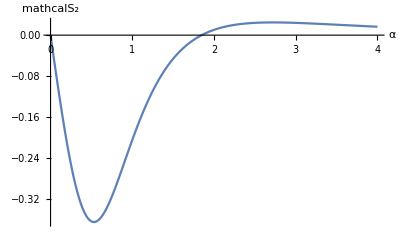

```mathematica
(* Plot of Subscript[S, 2] vs. α. *)

ListPlot[Transpose[{numericalAlpha,Subscript[numericalS, 2]}],Joined->True,AxesLabel-> {α,Subscript[mathcalS, 2]}]
```

```mathematica
(** Explicit representation of Subscript[S, 2] as a function of α and kcol, the solution of the collision condition Ω[kcol,1] = Ω[k+p,-1]. kcol is implicitly a function of α. **)

Subscript[S, 2,v3]=Simplify[Expand[Subscript[S, 2,v2]  //. n -> kcol - Subscript[μ, 0]]] /. Subscript[ω, j_]:> ω[Subscript[μ, 0]+j] //. Subscript[Q, 2,2] -> (1+Subscript[c, 0]^4+8 Subscript[c, 0]^2 Subscript[N, 2,2])/(16 Subscript[c, 0]^3)//. 
Subscript[Q, 2,0] -> -(-1+Subscript[c, 0]^4)/(4 Subscript[c, 0]^3)//.
Subscript[c, 2] ->  (3 Sinh[α]+4 Subscript[c, 0]^4 (Sinh[α]+4 Cosh[α] Subscript[N, 2,2])+Subscript[c, 0]^2 (3 Cosh[α]+8 Sinh[α] Subscript[N, 2,2])-2 Subscript[c, 0]^6 (Cosh[α]+12 Sinh[α] Subscript[N, 2,2]))/(8 Subscript[c, 0]^3 (Sinh[α]+Cosh[α] Subscript[c, 0]^2))//.Subscript[N, 2,2] -> (4 Subscript[c, 0]^2+Tanh[2 α]-3 Subscript[c, 0]^4 Tanh[2 α])/(16 Subscript[c, 0]^4-8 Subscript[c, 0]^2 Tanh[2 α]) //.   Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0])//. Subscript[c, 0] -> Sqrt[Tanh[α]]
```

-((Coth[α] (3 kcol (1+kcol)^2 Sign[kcol]^2 Tanh[kcol α]+kcol (1+kcol) (2+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]+2 Sign[kcol] Tanh[α]^(7/2) √(kcol Tanh[kcol α]) (-(16 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+3 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])+2 (1+kcol) Sign[kcol] √Tanh[α] √(kcol Tanh[kcol α]) (3+7 kcol+2 kcol^2-2 kcol (1+kcol) Sign[kcol]^2 Sign[1+kcol]^2 Tanh[kcol α] Tanh[(1+kcol) α])-Tanh[α]^3 (4 kcol (1+kcol)+kcol Sign[kcol]^2 Tanh[kcol α] ((96 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-15 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]))+2 Tanh[α]^(5/2) ((kcol (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))/(2 Tanh[α]^(3/2))+2 Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-(28 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+5 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])-Sign[kcol] √(kcol Tanh[kcol α]) (1+8 kcol+5 kcol^2-(16 (1+kcol) Sign[1+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(1+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+2 Tanh[α]^(3/2) ((kcol (2+3 kcol) Sign[kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α])/(2 Tanh[α]^(3/2))-(kcol (1+kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(2 Tanh[α]^(3/2))+3 Sign[kcol]^5 (kcol Tanh[kcol α])^(5/2) (-(4 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])-Sign[kcol] √(kcol Tanh[kcol α]) (-(4 kcol (2+kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) (5+8 kcol+kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α])-2 Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-1+2 kcol+kcol^2-(4 (1+kcol) Sign[1+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(1+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+Tanh[α] (((1+kcol) Sign[kcol]^3 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (kcol Tanh[kcol α])^(3/2))/Tanh[α]^(3/2)-1/Tanh[α]^(3/2)(1+kcol)^2 Sign[kcol] Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) √(kcol Tanh[kcol α]) Tanh[(1+kcol) α]+kcol^3 Sign[kcol]^6 Tanh[kcol α]^3 (-(4 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])-kcol Sign[kcol]^2 Tanh[kcol α] (-(4 kcol (2+kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) (11+14 kcol+kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α])-kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 (-1+2 kcol+kcol^2-(4 (1+kcol) Sign[1+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(1+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+kcol (2+kcol) (5+6 kcol+kcol^2-(4 (1+kcol) Sign[1+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(1+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+Tanh[α]^2 (((1+3 kcol) Sign[kcol] (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) √(kcol Tanh[kcol α]))/Tanh[α]^(3/2)+kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 (-(68 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+15 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])-2 kcol (-(2 (2+kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) (4+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])+kcol Sign[kcol]^2 Tanh[kcol α] (1-18 kcol-9 kcol^2+(32 (1+kcol) Sign[1+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(1+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(4 (Tanh[α]+kcol Sign[kcol]^2 Tanh[kcol α]+2 Sign[kcol] √Tanh[α] √(kcol Tanh[kcol α])-(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α])))